```mathematica
SetDirectory[NotebookDirectory[]];
<<"helpers.wls"

$PlotTheme = "Default";
frameLabelStyle[text_]:= Style[text, FontSize->12,FontColor->Gray];
frameTicksStyle = Directive[FontSize-> 8, FontColor-> Gray];
legendStyle [text_]:= Style[text, FontSize->12, FontColor->Gray];
plotLabelStyle[text_]:= Style[text, FontSize->14, FontColor->Gray];
cm = 72/2.54;
colorMap = 97;

thesisImages = FileNameJoin[{NotebookDirectory[], "..", "..", "thesis","chapters","img"}];
```

## Find Simulation Parameters

```mathematica
Needs["DatabaseLink`"];
```

```mathematica
<<"../classify-smi/helpers-scores.wls";
<<"../classify-smi/helpers-data.wls";
<<"../classify-smi/scores.wls";
```

```mathematica
conn = OpenSQLConnection[JDBC["PostgreSQL","127.0.0.1/teodor"],"Username"->"teodor"];
```

```mathematica
smi2014records = SmiUnpackRecords@@@SQLExecute[conn, "select 
source_data_set, 
source_track_id, 
track_start, 
track_end, 
category, 
levels_order, 
track_size,
frame_dim_int, 
frame_dim_img, 
scores, 
levels, 
data_int, 
data_img,
levels_old
from smidata
where 
    dataset_id = 13
and category = 1
order by source_data_set, source_track_id"
];
```

```mathematica
simIfB05 = <||>;
```

```mathematica
(simIfB05[#] = SmiUnpackRecords@@@SQLExecute[conn, "select 
source_data_set, 
source_track_id, 
track_start, 
track_end, 
category, 
levels_order, 
track_size,
frame_dim_int, 
frame_dim_img, 
scores, 
levels, 
data_int, 
data_img,
levels_old
from smidata
where 
    dataset_id = 37
and source_data_set like '%I_"<>numStr[#]<>"%fB_00005%g_250%'
order by source_data_set, source_track_id"] )&/@ Range[20, 80, 20];
```

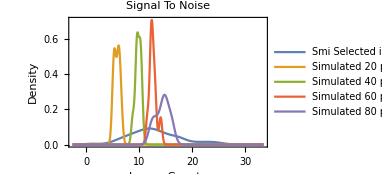

```mathematica
Block[{img},
img = SmoothHistogram[{
SignalToNoiseL1/@smi2014records,
SignalToNoiseL1/@simIfB05[20],
SignalToNoiseL1/@simIfB05[40],
SignalToNoiseL1/@simIfB05[60],
SignalToNoiseL1/@simIfB05[80]},
PlotLabel->plotLabelStyle["Signal To Noise"],
Frame-> True,
FrameTicksStyle->frameTicksStyle,
FrameLabel-> (frameLabelStyle/@{"Image Counts", "Density"}),
PlotLegends->(legendStyle/@{
"Smi Selected in 2014 L1",
"Simulated 20 photons",
"Simulated 40 photons",
"Simulated 60 photons",
"Simulated 80 photons"}),
ImageSize->10cm];
Export[FileNameJoin[{thesisImages, "methods-simulations-signal-to-noise.pdf"}], img];
img
]
```

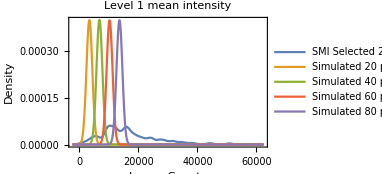

```mathematica
Block[{img},
img = SmoothHistogram[{
#[[scoresI]]["cts_mean_lvl_1"]&/@smi2014records,
#[[scoresI]]["cts_mean_lvl_1"]&/@simIfB05[20],
#[[scoresI]]["cts_mean_lvl_1"]&/@simIfB05[40],
#[[scoresI]]["cts_mean_lvl_1"]&/@simIfB05[60],
#[[scoresI]]["cts_mean_lvl_1"]&/@simIfB05[80]},
1000,
PlotLabel->plotLabelStyle["Level 1 mean intensity"],
Frame-> True,
FrameLabel-> (frameLabelStyle/@{"Image Counts", "Density"}),
FrameTicksStyle->frameTicksStyle,
PlotLegends->(legendStyle/@{"SMI Selected 2014",
"Simulated 20 photons",
"Simulated 40 photons",
"Simulated 60 photons",
"Simulated 80 photons"}),
PlotRange->All,
ImageSize->10cm];
Export[FileNameJoin[{thesisImages, "methods-simulations-l1-intensity.pdf"}],img];
img
]
```

```mathematica
simBfI80 = <||>;
```

```mathematica
(simBfI80[#] = SmiUnpackRecords@@@SQLExecute[conn, "select 
source_data_set, 
source_track_id, 
track_start, 
track_end, 
category, 
levels_order, 
track_size,
frame_dim_int, 
frame_dim_img, 
scores, 
levels, 
data_int, 
data_img,
levels_old
from smidata
where 
    dataset_id = 37
and source_data_set like '%I_00080%fB_"<> numStr[#]<>"-q_0_92-c_0_02-g_250-r_50-f_12_7-sigma_1_06157%'
order by source_data_set, source_track_id"] )&/@ Range[5, 30,5];
```

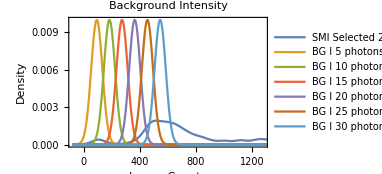

```mathematica
Block[{img},
img = SmoothHistogram[{
Mean/@smi2014records[[All,9,All, 6]],
Mean/@simBfI80[5][[All, 9, All, 6]],
Mean/@simBfI80[10][[All, 9, All, 6]],
Mean/@simBfI80[15][[All, 9, All, 6]],
Mean/@simBfI80[20][[All, 9, All, 6]],
Mean/@simBfI80[25][[All, 9, All, 6]],
Mean/@simBfI80[30][[All, 9, All, 6]]
}, 40,
Frame-> True,
FrameTicksStyle->frameTicksStyle,
FrameLabel->(frameLabelStyle/@{"Image Counts","Density"}),
PlotLabel->plotLabelStyle["Background Intensity"],
PlotLegends->(legendStyle/@{
"SMI Selected 2014",
"BG I 5 photons",
"BG I 10 photons",
"BG I 15 photons",
"BG I 20 photons",
"BG I 25 photons",
"BG I 30 photons"
}),
ImageSize->10cm];
Export[FileNameJoin[{thesisImages, "methods-simulations-background-int.pdf"}], img];
img
]
```

Based on the histogram of the level 1 signal to noise ratio and level 1 intensity the best value for the fluorophore intensity is 80 photons

Based on the histogram of the background intensity values the best value for the background is 30 photons

Both of these values are at gain 250, A/D factor of 12.7, quantum efficiency of 0.92, spurious charge of 0.02, and read out noise with standard deviation of 50.

## Thesis images

```mathematica
frame = addNoise[{{GenerateFrame[Table[1, 9], 
Table[120, 9], Flatten[
Table[
{25*x,25*y},
{x, 1, 3}, {y, 1, 3}], 1],
30, 100]
}}];
```

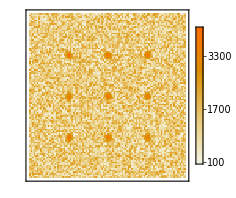

```mathematica
Block[{img},
img = MatrixPlot[First@First@frame,
FrameTicks-> None,
PlotRange->All,
PlotLegends->Automatic,
ImageSize->7cm];
Export[FileNameJoin[{thesisImages,"methods-simulations-typical-frame.pdf"}], img];
img]
```

```mathematica
frameSingleFluorophore = GenerateFrame[{1}, {100},{{9.5, 9.5}}, 30, 20];
```

```mathematica
nframeSingleFluorophore  = First@First@addNoise[{{frameSingleFluorophore }}];
```

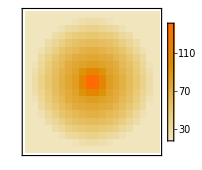
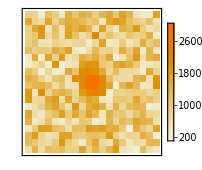

{{1},{{1},118,{{515.727,645.552,676.845,458.035,429.204,458.102,88,624.651,271.525,469.084,485.95,483.989,676.932},98,{1}}}}[1,1,1,1]
 |  |  |  |

```mathematica
Block[{img},
img = Row[{
MatrixPlot[frameSingleFluorophore,
FrameTicks-> None,
PlotRange->All,
PlotLegends->Automatic,
ImageSize->6cm],
MatrixPlot[nframeSingleFluorophore,
FrameTicks-> None,
PlotRange->All,
PlotLegends->Automatic,
ImageSize->6cm]
}];
Export[FileNameJoin[{thesisImages,"methods-simulations-before-after-noise.pdf"}], img];
img]
```

## Refining Track Selection Process

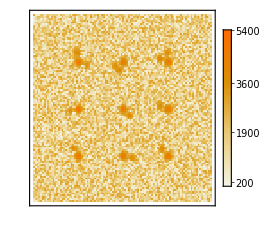

```mathematica
Block[{data, img},
data = <<"data.bin/rtsp-neighbour-lvl_00220-I_00080-fB_00030-q_0.92-c_0.02-g_250-r_50-f_12.7-sigma_1.06157.bin";
img = MatrixPlot[
data[[1]],
FrameTicks->None,
PlotLegends->Automatic,
PlotRange->All,
ImageSize-> 8cm
];
Export[FileNameJoin[{thesisImages, "simulations-refining-neightbour.pdf"}], img];
img
]
```

```mathematica
<<"../classify-smi/helpers-scores.wls";
<<"../classify-smi/helpers-data.wls";
<<"../classify-smi/scores.wls";
```

```mathematica
Needs["DatabaseLink`"];
```

```mathematica
conn = OpenSQLConnection[JDBC["PostgreSQL","teodor-desktop/teodor"],"Username"->"teodor", "Password"-> "4HWZQ3y60gKKcTNp"];
```

```mathematica
track = 
SmiUnpackRecords@@@ SQLExecute[conn, "select 
source_data_set, 
source_track_id, 
track_start, 
track_end, 
category, 
levels_order, 
track_size,
frame_dim_int, 
frame_dim_img, 
scores, 
levels, 
data_int, 
data_img,
levels_old
from smidata
where
   source_data_set like '%rtsp-end-lvl3%'
order by id
"
];
```

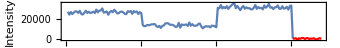

```mathematica
Block[{img},
img = ListLinePlot[{
#[[dataIntI, 1;;#[[trackEndI]] - #[[trackStartI]] +2, {1, 2}]],
#[[dataIntI, #[[trackEndI]] - #[[trackStartI]] +2;;-1, {1, 2}]]
},
PlotStyle->{ColorData[colorMap][1], Red},
AspectRatio-> 1/8,
PlotRange-> All,
ImageSize->12cm,
Frame-> True,
FrameTicksStyle->frameTicksStyle,
FrameLabel->(frameLabelStyle/@{"FrameId","Intensity" })
]&@ track[[2]];
Export[FileNameJoin[{thesisImages, "simulations-refining-endlvl3-track.pdf"}], img];
img
]
```